## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; Q=0.91; r1 = 3.0; mu = 0.01;
```

```mathematica
winit=(3.3-0.00005*I)
```

3.3-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
(* winit = 3.3 - 0.00005*I for qscal=6.5 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 6.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

3.2873+0.0150042 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
qscal = 6.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

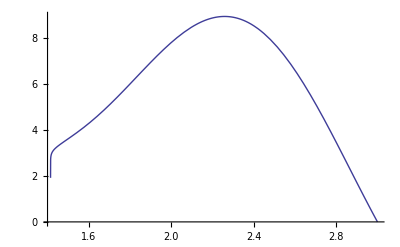

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(3.3-0.00005*I);
ie=0;While[ie<11,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 6.5 +ie; r0=rp+10^(-6); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal;
winit=wres+0.4;
ie=ie+1
]
t1r=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,10}]
t2r=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,10}]
```

{{6.5,3.2873},{7.5,3.6732},{8.5,4.0539},{9.5,4.43034},{10.5,4.80319},{11.5,5.17294},{12.5,5.53998},{13.5,5.90464},{14.5,6.26716},{15.5,6.62775},{16.5,6.9866}}

{{6.5,0.0150042},{7.5,0.0188315},{8.5,0.0225359},{9.5,0.0260917},{10.5,0.0294932},{11.5,0.032744},{12.5,0.0358523},{13.5,0.0388278},{14.5,0.0416807},{15.5,0.0444207},{16.5,0.0470569}}

```mathematica
winit=(7.0-0.00005*I);
ie=0;While[ie<11,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 16.5 +ie; r0=rp+10^(-6); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal;
winit=wres+0.36;
ie=ie+1
]
t1r2=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,10}]
t2r2=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,10}]
```

{{16.5,6.9866},{17.5,7.34385},{18.5,7.69964},{19.5,8.05407},{20.5,8.40726},{21.5,8.75929},{22.5,9.11023},{23.5,9.46016},{24.5,9.80913},{25.5,10.1572},{26.5,10.5044}}

{{16.5,0.0470569},{17.5,0.0495976},{18.5,0.0520505},{19.5,0.0544223},{20.5,0.0567191},{21.5,0.0589466},{22.5,0.0611095},{23.5,0.0632125},{24.5,0.0652596},{25.5,0.0672543},{26.5,0.0692}}

```mathematica
winit=(10.5-0.00005*I);
ie=0;While[ie<6,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 26.5 +ie; r0=rp+10^(-6); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal;
winit=wres+0.36;
ie=ie+1
]
t1r3=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,5}]
t2r3=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,5}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{26.5,10.5044},{27.5,10.8509},{28.5,11.195},{29.5,11.5413},{30.5,11.8847},{31.5,12.2293}}

{{26.5,0.0692003},{27.5,0.0710987},{28.5,0.0728938},{29.5,0.0743978},{30.5,0.0774899},{31.5,0.0781662}}

```mathematica
(*The imaginary part vs the radius*)
```

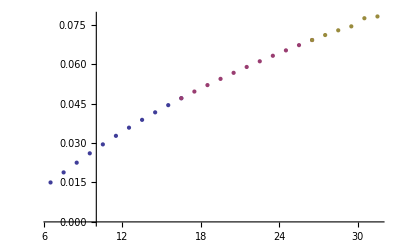

```mathematica
ListPlot[{t2r,t2r2,t2r3},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

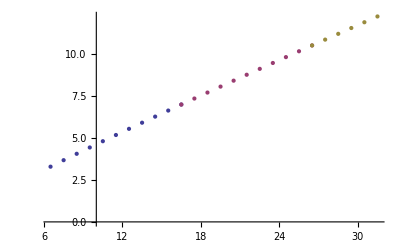

```mathematica
ListPlot[{t1r,t1r2,t1r3}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.1/max/Q=0.9/R.dat",Join[t1r,t1r2,t1r3]]
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.1/max/Q=0.9/I.dat",Join[t2r,t2r2,t2r3]]
```

/home/h/skoli/pt/rnef/mathematica/q/mu0.1/max/Q=0.9/R.dat

/home/h/skoli/pt/rnef/mathematica/q/mu0.1/max/Q=0.9/I.dat